```mathematica
({{10-x, x}})×({{1, 0, 0}, {0, 1, 0}} )×({{0}, {1500}, {2000}})
```

Thread::tdlen: {{10-x,x}} {{1,0,0},{0,1,0}} {{0},{1500},{2000}} 中长度不相等的对象无法合并.

Thread::tdlen: {{10-x,x}} {{1,0,0},{0,1,0}} {{0},{1500},{2000}} 中长度不相等的对象无法合并.

{{10-x,x}} {{1,0,0},{0,1,0}} {{0},{1500},{2000}}

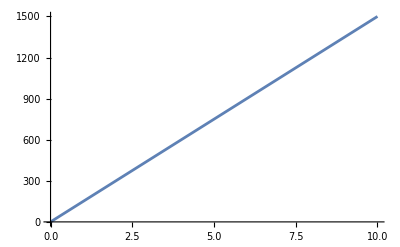

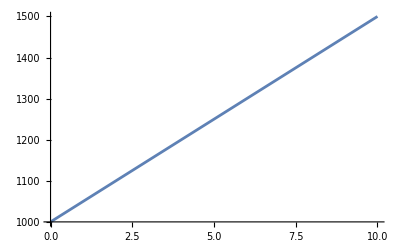

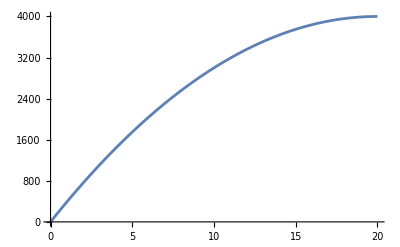

```mathematica
{{10-x,x}} {{1,0,0},{0,1,0}} {{0},{1500},{2000}}

Plot[150x,{x,0,10}]
Plot[1500+50(x-10),{x,0,10}]
Plot[-10x^2+400x,{x,0,20}]
```

```mathematica
Piecewise[{{150x,0<x<10},{1500+50(x-10)},10<x<20}]
```

Piecewise::pairs: Piecewise 的第一个参数 {{150 x,0<x<10},{1500+50 (-10+x)},10<x<20} 不是由数对组成的列表.

Piecewise[{{150 x,0<x<10},{1500+50 (x-10)},10<x<20}]

```mathematica
Linelegend[{Blue, Red}, {"FEM_Solution","Exact_Solution"}]
```

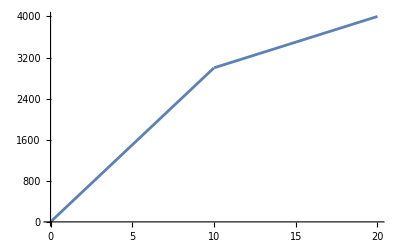

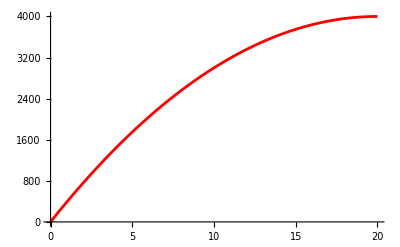

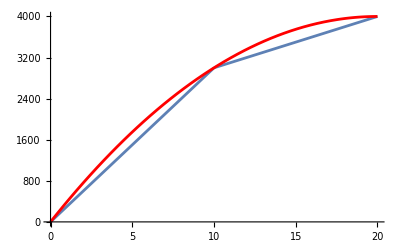

Piecewise::pairs: Piecewise 的第一个参数 {{0.122571,True},{2000.04},False} 不是由数对组成的列表.

Piecewise::pairs: Piecewise 的第一个参数 {{122.572,True},{2040.86},False} 不是由数对组成的列表.

General::stop: 在本次计算中，Piecewise::pairs 的进一步输出将被抑制.

```mathematica
p1=Plot[Piecewise[{{300x,0<x<10},{3000+100(x-10),10<x<20}}], {x,0,20},PlotLegends->Linelegend["FEM_Solution"]]
p2=Plot[{-10x^2+400x},{x,0,20}, PlotStyle->Red, PlotLegends->Linelegend["Exact_solution"]]
Show[p1,p2, PlotLegends->Linelegend]
```

```mathematica
Linelegend[{Blue, Red}, {"FEM_Solution","Exact_Solution"}]
p1=Plot[Piecewise[{{300x,0<x<10},{3000+100(x-10),10<x<20}}], {x,0,20},PlotLegends->LineLegend["FEM_Solution"]]
p2=Plot[{-10x^2+400x},{x,0,20}, PlotStyle->Red, PlotLegends->LineLegend["Exact_solution"]]
Show[p1,p2, PlotLegends->Linelegend]
```

Linelegend[{RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{FEM_Solution,Exact_Solution}]

-Graphics-

-Graphics-

-Graphics-

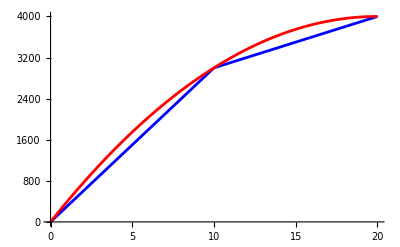

```mathematica
p1=Plot[Piecewise[{{300 x,0<x<10},{3000+100 (x-10),10<x<20}}],{x,0,20},PlotStyle->Blue];

p2=Plot[-10 x^2+400 x,{x,0,20},PlotStyle->Red];

Show[p1,p2,PlotLegends->LineLegend[{Blue,Red},{"FEM Solution","Exact Solution"}]]
```

```mathematica
Show[%71,AxesStyle->Gray]
```

-Graphics-

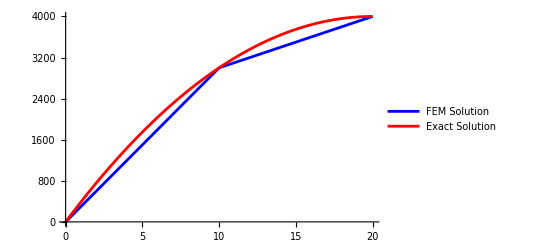

```mathematica
Plot[{Piecewise[{{300 x,0<x<10},{3000+100 (x-10),10<x<20}}],-10 x^2+400 x},{x,0,20},PlotStyle->{Blue,Red},PlotLegends->{"FEM Solution","Exact Solution"}]
```

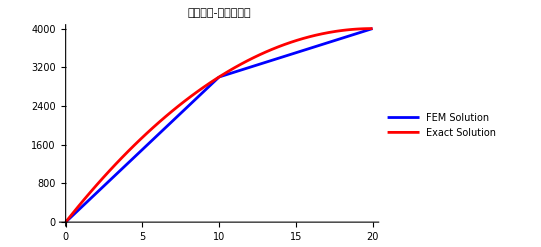

```mathematica
Show[%73,PlotLabel->HoldForm[有限元解-精确温度场],LabelStyle->{9,GrayLevel[0]}]
```

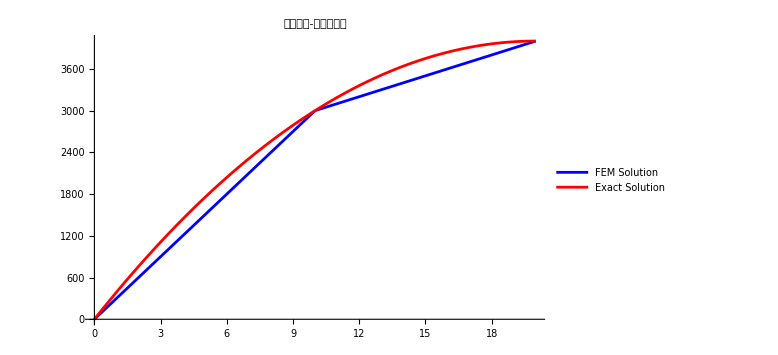

```mathematica
Show[%74,ImageSize->Large]
```

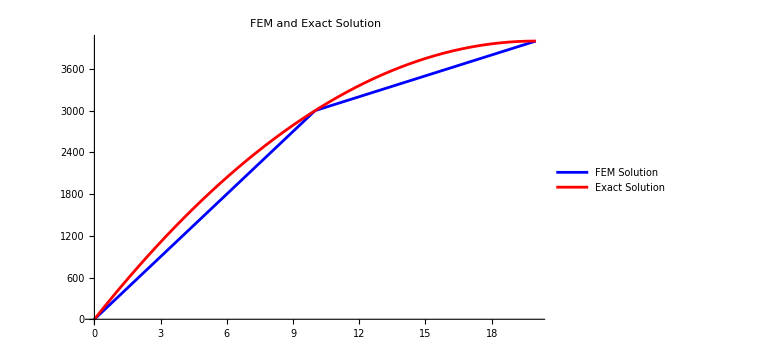

```mathematica
Show[%75,PlotLabel->HoldForm[FEM and Exact Solution],LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["/Users/huangbingqi/Documents/2024_Spring_Semester/FEM/FEM/HW_10/FEM and Exact Solution_2e.png",%77,"PNG"]
```

```mathematica
"/Users/huangbingqi/Documents/2024_Spring_Semester/FEM/FEM/HW_10/FEM and Exact Solution_2e.png"
```

/Users/huangbingqi/Documents/2024_Spring_Semester/FEM/FEM/HW_10/FEM and Exact Solution_2e.png

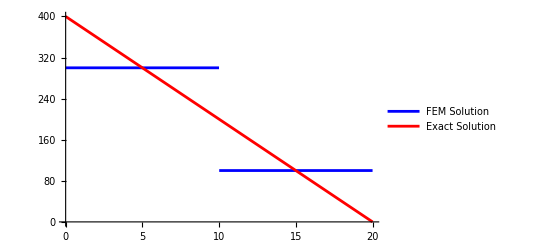

```mathematica
Plot[{Piecewise[{{300 ,0<x<10},{100 ,10<x<20}}],-20 x+400 },{x,0,20},PlotStyle->{Blue,Red},PlotLegends->{"FEM Solution","Exact Solution"}]
```

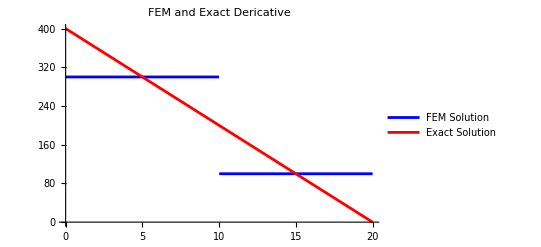

```mathematica
Show[%80,PlotLabel->HoldForm[FEM and Exact Dericative],LabelStyle->{GrayLevel[0]}]
```

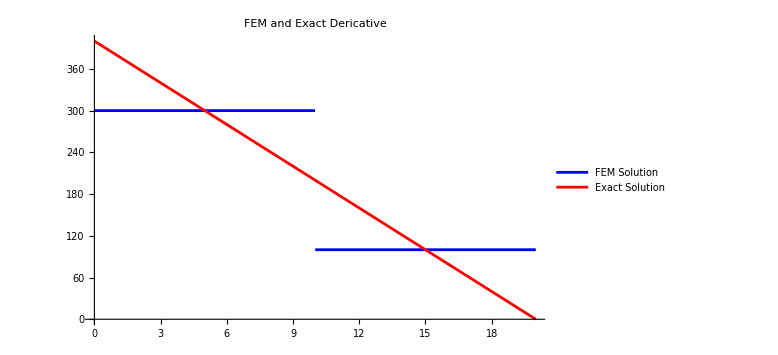

```mathematica
Show[%81,ImageSize->Large]
```

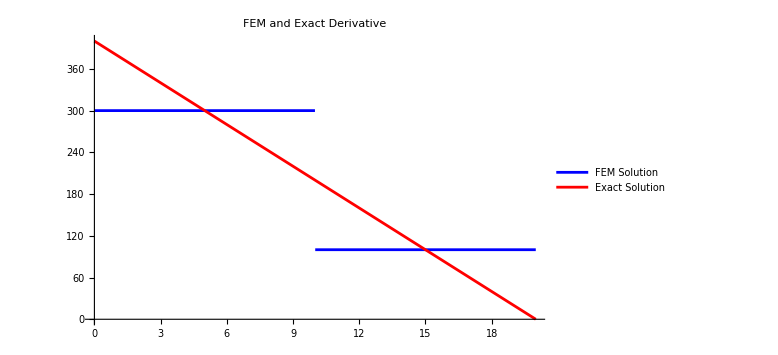

```mathematica
Show[%82,PlotLabel->HoldForm[FEM and Exact Derivative],LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["/Users/huangbingqi/Documents/2024_Spring_Semester/FEM/FEM/HW_10/FEM_Exact_Derivative_2e.png",%83,"PNG"]
```

/Users/huangbingqi/Documents/2024_Spring_Semester/FEM/FEM/HW_10/FEM_Exact_Derivative_2e.png